## HMQC spectrum of 13C-C1 labelled Glucose

```mathematica
SetDirectory[NotebookDirectory[] <> "/.."]
```

/Users/mu3q/GitHub/NMRprocess2

```mathematica
<<NMRProcess2`
```

NMR Processing
Version 2.0.0
(c)2016 Marcel Utz
marcel.utz@southampton.ac.uk

## Load data

```mathematica
rawfid= ReadBruker["ExampleData/10/ser"]
```

-|Fid..1--

Only the raw NMR acquisition data is loaded, without any information about dwell time, etc. The time domain structure must be set explicitly:

```mathematica
hmqcfid=SetTimeDomain[rawfid,{4096,256}]
```

-|Fid..2--

## Fourier Transform

We perform a 2D FT assuming the data has been acquired in States-TPPI hypercomplex mode.

```mathematica
spect=StatesFFT2[hmqcfid,Phase2->-2.25,Phase1->-0.5,SI1->1024,SI2->4096]
```

-|Fid..2--

In order to obtain calibrated plots, we need to set the spectral width (in ppm) and the offsets:

```mathematica
spect=SetProp[spect,Offset,{-0.8,96.6}];
spect=SetProp[spect,SpectralWidth,{20,90}];
```

## Plots

A full 2D spectrum can be plotted with NMRContourPlot:

```mathematica
NMRContourPlot[spect]
```

-Graphics-

The contour levels are automatically set to 10%, 20%, ... of the highest point in the spectrum.
In the present case, we are only interested in a subregion of the spectrum. Crop[]  can be used to reduce the
data:

```mathematica
overview=Crop[spect,{{6.,2.},{120.,60.}}]
```

-|Fid..2--

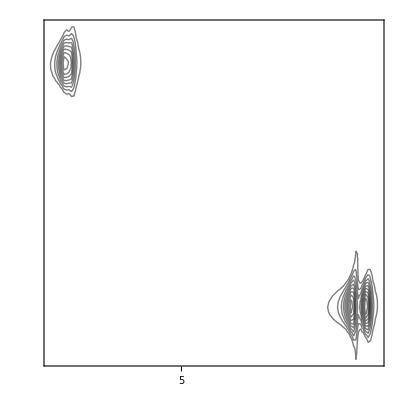

```mathematica
NMRContourPlot[overview]
```

Rows and columns can be extracted from 2D spectra, and plotted using PlotNMR1D. Note that the resulting 1D spectrum is interpolated as needed, i.e., any value for the row position can be indicated, not just the ones digitally represented by the underlying data.

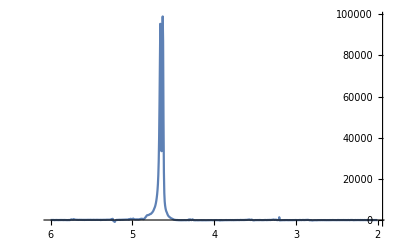

```mathematica
PlotNMR1D[ExtractRow[overview,98.3],PlotRange->All]
```

ExtractRow[ ] can handle lists of row indices:

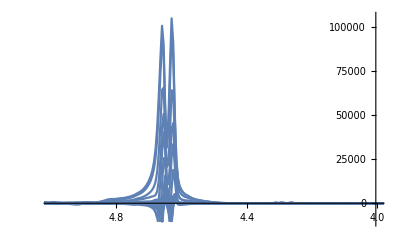

```mathematica
Show[ PlotNMR1D[ExtractRow[overview,Range[96.,100.,0.2]],PlotRange->{{-5,-4},Max[overview[spectrum]]{-0.1,1}} ]]
```